## Método de la bisección

```mathematica
y[x_]:=x^2-2;
```

```mathematica
x1 = 1;
x2 = 1.5;

intervalos = {{x1,x2}};
Do[
x3 = Mean[{x1,x2}];
If[y[x1]*y[x3]<0,
{x1,x2} = {x1,x3}
,
{x1,x2} = {x3,x2}
];
AppendTo[intervalos,{x1,x2}]; (* Añado {x1,x2} a la lista *)
,
10 (* Número de repeticiones *)
];
```

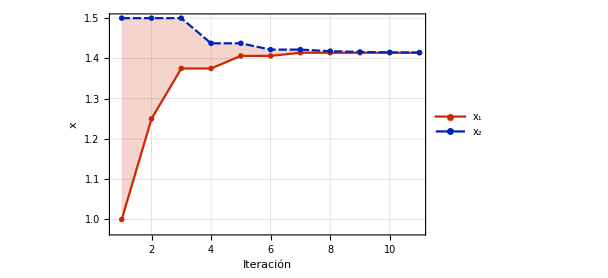

```mathematica
ListLinePlot[
Transpose[intervalos],
PlotRange->All,
Filling->{1->{2}},
Frame->True,
ImageSize->450,
BaseStyle->FontSize->13,
FrameLabel->{Style["Iteración",15], Style["x",15]},
PlotTheme->"Monochrome",
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.14, 0.7000000000000001]},
GridLines->Automatic,
PlotLegends->Placed[
LineLegend[
{"x_1","x_2"},
LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),
LabelStyle->11
],
{Right,Bottom}
]
]
```

## Método del punto falso

```mathematica
x1 = 1;
x2 = 1.5;
x3 = (x1 y[x2]-x2 y[x1])/(y[x2]-y[x1]);

intervalos = {{x1,x2}};
Do[
If[(Abs[y[x1]*y[x3]]≥0.00001) &&(x1 ≠ x2),
x3 = (x1 y[x2]-x2 y[x1])/(y[x2]-y[x1]);

If[y[x1]*y[x3]<0,
{x1,x2} = {x1,x3}
,
{x1,x2} = {x3,x2}
],
{x1,x2} = {x3,x3}
];
AppendTo[intervalos,{x1,x2}]; 
,
10
];
```

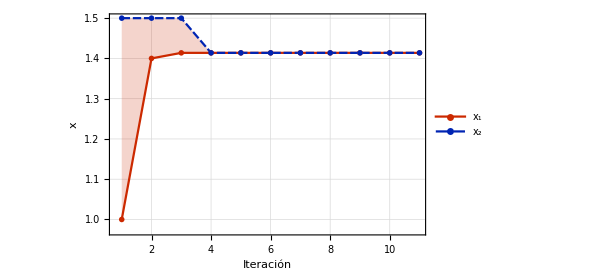

```mathematica
ListLinePlot[
Transpose[intervalos],
PlotRange->All,
Filling->{1->{2}},
Frame->True,
ImageSize->450,
BaseStyle->FontSize->13,
FrameLabel->{Style["Iteración",15], Style["x",15]},
PlotTheme->"Monochrome",
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.14, 0.7000000000000001]},
GridLines->Automatic,
PlotLegends->Placed[
LineLegend[
{"x_1","x_2"},
LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),
LabelStyle->11
],
{Right,Bottom}
]
]
```